```mathematica
F[t_]:=-Sin[Pi t];
∫_0^2 (F[t])^2 ⅆt
FourierCoefficient[-Sin[t],t,n]
```

1

Piecewise[{{-ⅈ/2, n==-1}, {ⅈ/2, n==1}, {0, True}}]

```mathematica
G[t_]:=∑_(k=-100)^-1 Sin[Pi k/4]/(Pi k)*Exp[-I k Pi/2]*Exp[I k Pi t/2 ]+∑_(k=1)^100 Sin[Pi k/4]/(Pi k)*Exp[-I k Pi/2]*Exp[I k Pi t/2]
```

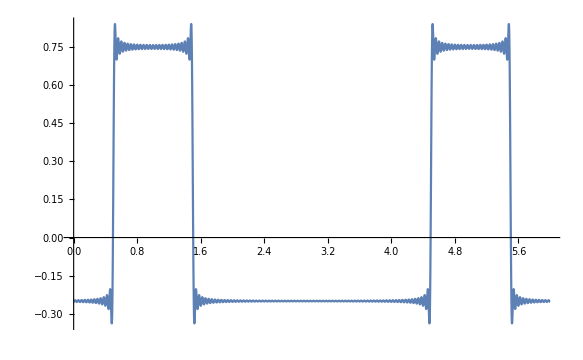

```mathematica
Plot[G[t],{t,0,6}]
```

```mathematica
∑_(k=1)^Infinity (Sin[0.25 Pi k]/(Pi k))^2
```

0.09375+0. ⅈ

```mathematica
F1[t]:=ⅇ^(2t)*UnitStep[-t]
H[t]:=UnitStep[t-1]
```

```mathematica
Convolve[F1[t],H[t],t,y]
```

Piecewise[{{1/2, y≥1}, {1/2 ⅇ^(-2+2 y), True}}]

```mathematica
W=2 Pi/3
```

(2 π)/3

```mathematica
X[t_]:=0.5*Exp[I 3 W t]+0.5*Exp[-I  3 W t]
```

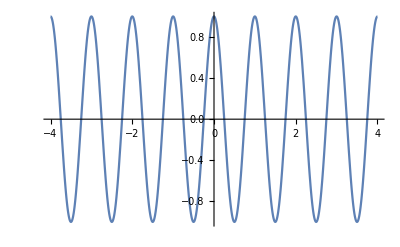

```mathematica
Plot[X[t],{t,-4,4}]
```